```mathematica
Plot3D[(ArcCos[x]/Sqrt[1-x^2])(1-y^2)-(Sqrt[1-x^2]-x ArcCos[x])/(1-x^2)^(1.5)(1-y*x),{x,0,2Pi},{y,0,1}]
```

-Graphics3D-

```mathematica
Define two vectors on the sphere in 2D, we linearize around q
```

```mathematica
x[t_]:={Cos[t],Sin[t]}
```

```mathematica
q[s_]:={Cos[s],Sin[s]}
```

```mathematica
x'[t]
```

{-Sin[t],Cos[t]}

```mathematica
g[t_,s_]=q[s].x[t]
```

Cos[s] Cos[t]+Sin[s] Sin[t]

```mathematica
g[1,2]
```

Cos[1] Cos[2]+Sin[1] Sin[2]

```mathematica
f[t_,s_]:=ArcCos[g[t,s]]/Sin[ArcCos[g[t,s]]]
```

```mathematica
f'[t]
```

(ArcCos[Cos[s] Cos[t]+Sin[s] Sin[t]] (Cos[t] Sin[s]-Cos[s] Sin[t]) (Cos[s] Cos[t]+Sin[s] Sin[t]))/(1-(Cos[s] Cos[t]+Sin[s] Sin[t])^2)^(3/2)-(Cos[t] Sin[s]-Cos[s] Sin[t])/(1-(Cos[s] Cos[t]+Sin[s] Sin[t])^2)

```mathematica
h is the Log_x of q
```

```mathematica
h[t_,s_]:=(x[t]-q[s]g[t,s])f[t,s]
```

```mathematica
D[h[t,s],t]
```

{(ArcCos[Cos[s] Cos[t]+Sin[s] Sin[t]] (Cos[t] Sin[s]-Cos[s] Sin[t]) (Cos[s] Cos[t]+Sin[s] Sin[t]) (Cos[t]-Cos[s] (Cos[s] Cos[t]+Sin[s] Sin[t])))/(1-(Cos[s] Cos[t]+Sin[s] Sin[t])^2)^(3/2)-((Cos[t] Sin[s]-Cos[s] Sin[t]) (Cos[t]-Cos[s] (Cos[s] Cos[t]+Sin[s] Sin[t])))/(1-(Cos[s] Cos[t]+Sin[s] Sin[t])^2)+(ArcCos[Cos[s] Cos[t]+Sin[s] Sin[t]] (-Sin[t]-Cos[s] (Cos[t] Sin[s]-Cos[s] Sin[t])))/(√(1-(Cos[s] Cos[t]+Sin[s] Sin[t])^2)),(ArcCos[Cos[s] Cos[t]+Sin[s] Sin[t]] (Cos[t] Sin[s]-Cos[s] Sin[t]) (Cos[s] Cos[t]+Sin[s] Sin[t]) (Sin[t]-Sin[s] (Cos[s] Cos[t]+Sin[s] Sin[t])))/(1-(Cos[s] Cos[t]+Sin[s] Sin[t])^2)^(3/2)-((Cos[t] Sin[s]-Cos[s] Sin[t]) (Sin[t]-Sin[s] (Cos[s] Cos[t]+Sin[s] Sin[t])))/(1-(Cos[s] Cos[t]+Sin[s] Sin[t])^2)+(ArcCos[Cos[s] Cos[t]+Sin[s] Sin[t]] (Cos[t]-Sin[s] (Cos[t] Sin[s]-Cos[s] Sin[t])))/(√(1-(Cos[s] Cos[t]+Sin[s] Sin[t])^2))}

```mathematica
This is the Jacobian of the Log map of {A,B} around x[t]
```

```mathematica
NormJ[t_,s_]=Norm[D[h[t,s],t],2]
```

√(Abs[(ArcCos[Cos[s] Cos[t]+Sin[s] Sin[t]] (Cos[t] Sin[s]-Cos[s] Sin[t]) (Cos[s] Cos[t]+Sin[s] Sin[t]) (Cos[t]-Cos[s] (Cos[s] Cos[t]+Sin[s] Sin[t])))/(1-(Cos[s] Cos[t]+Sin[s] Sin[t])^2)^(3/2)-((Cos[t] Sin[s]-Cos[s] Sin[t]) (Cos[t]-Cos[s] (Cos[s] Cos[t]+Sin[s] Sin[t])))/(1-(Cos[s] Cos[t]+Sin[s] Sin[t])^2)+(ArcCos[Cos[s] Cos[t]+Sin[s] Sin[t]] (-Sin[t]-Cos[s] (Cos[t] Sin[s]-Cos[s] Sin[t])))/(√(1-(Cos[s] Cos[t]+Sin[s] Sin[t])^2))]^2+Abs[(ArcCos[Cos[s] Cos[t]+Sin[s] Sin[t]] (Cos[t] Sin[s]-Cos[s] Sin[t]) (Cos[s] Cos[t]+Sin[s] Sin[t]) (Sin[t]-Sin[s] (Cos[s] Cos[t]+Sin[s] Sin[t])))/(1-(Cos[s] Cos[t]+Sin[s] Sin[t])^2)^(3/2)-((Cos[t] Sin[s]-Cos[s] Sin[t]) (Sin[t]-Sin[s] (Cos[s] Cos[t]+Sin[s] Sin[t])))/(1-(Cos[s] Cos[t]+Sin[s] Sin[t])^2)+(ArcCos[Cos[s] Cos[t]+Sin[s] Sin[t]] (Cos[t]-Sin[s] (Cos[t] Sin[s]-Cos[s] Sin[t])))/(√(1-(Cos[s] Cos[t]+Sin[s] Sin[t])^2))]^2)

```mathematica
NormJ[.1,.32]
```

1.

```mathematica
NormJ[-.1,.32]
```

1.

```mathematica
NormJ[0,0]
```

Power::infy: Infinite expression 1/0^3/2 encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/√0 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

Indeterminate

```mathematica
Plot3D[NormJ[t,s],{t,-Pi,Pi},{s,-Pi,Pi}]
```

Power::infy: Infinite expression 1/0.^3/2 encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/√0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

-Graphics3D-

```mathematica
Table[NormJ[t,s],{t,-1,1},{s,-1,1}]
```

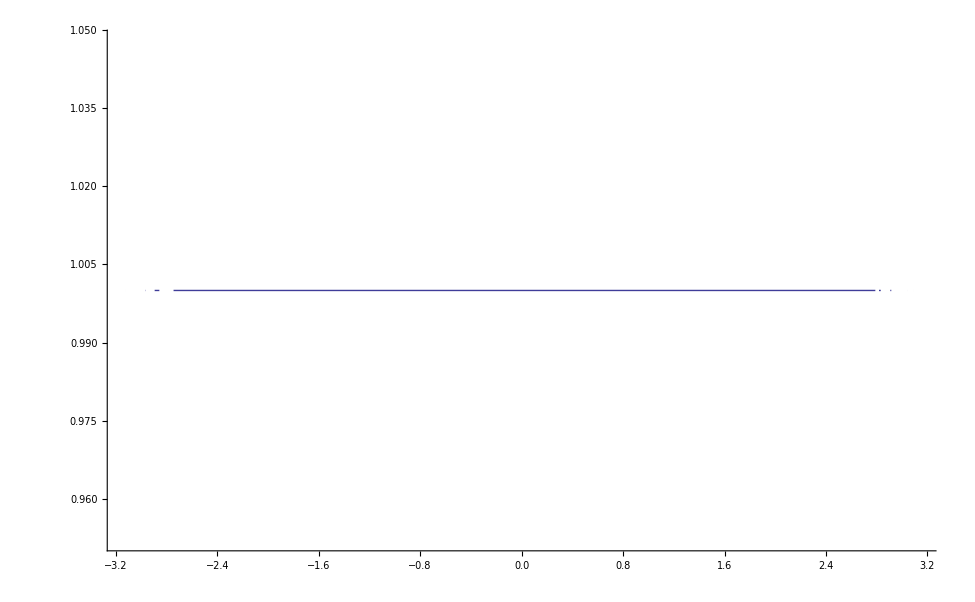

```mathematica
Plot[NormJ[t,0],{t,-Pi,Pi}]
```